```mathematica
(* Matrix power for Fibonacci computation. Compared to native Fibonacci *)
ℳ={{1,1}, {1,0}};
ℳ//MatrixForm
```

(1 | 1
1 | 0)

```mathematica
MatrixPower[ℳ,10-1]//MatrixForm
```

(55 | 34
34 | 21)

```mathematica
n=1000
```

1000

```mathematica
t1=AbsoluteTiming[MatrixPower[ℳ,n][[1]][[2]]]
```

{0.000389,43466557686937456435688527675040625802564660517371780402481729089536555417949051890403879840079255169295922593080322634775209689623239873322471161642996440906533187938298969649928516003704476137795166849228875}

```mathematica
t2=AbsoluteTiming[Fibonacci[n]]
```

{0.000054,43466557686937456435688527675040625802564660517371780402481729089536555417949051890403879840079255169295922593080322634775209689623239873322471161642996440906533187938298969649928516003704476137795166849228875}

```mathematica
t1[[1]]/t2[[1]]
```

7.2037

```mathematica
ts=Table[t1=AbsoluteTiming[MatrixPower[ℳ,n-1][[1]][[2]]]; t2=AbsoluteTiming[Fibonacci[n]];{n,t1[[1]]/t2[[1]]}, {n, 90, 10000}]
```

```mathematica
MaximalBy[ts, Last]
MinimalBy[ts, Last]
```

{{91,110.}}

{{357,1.50909}}

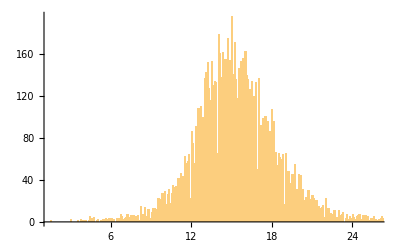

```mathematica
Histogram[ts[[All,2]], Ceiling[Length[ts]/10]]
```